{{s→InterpolatingFunction[{{0.,100.}},<>],i→InterpolatingFunction[{{0.,100.}},<>],r→InterpolatingFunction[{{0.,100.}},<>]}}

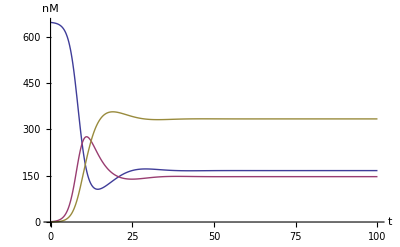

```mathematica
sol1=NDSolve[{s'[t]==(.11)*r[t]-(.0015)*s[t]*i[t], i'[t]== (.0015)*s[t]*i[t]-(.25)*i[t],r'[t]==(.25)*i[t]-(.11)*r[t], s[0]==647,i[0]==1,r[0]==0},{s,i,r},{t,0,100}]

Plot[Evaluate[{s[t],i[t],r[t]}/.sol1],{t,0,100},AxesLabel->{t,nM}]
```

{{s→InterpolatingFunction[{{0.,100.}},<>],i→InterpolatingFunction[{{0.,100.}},<>],r→InterpolatingFunction[{{0.,100.}},<>]}}

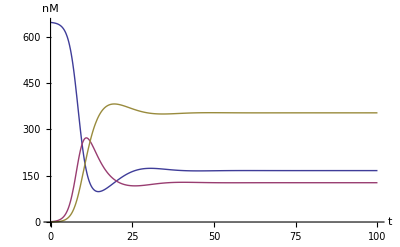

```mathematica
sol1=NDSolve[{s'[t]==(.09)*r[t]-(.0015)*s[t]*i[t], i'[t]== (.0015)*s[t]*i[t]-(.25)*i[t],r'[t]==(.25)*i[t]-(.09)*r[t], s[0]==647,i[0]==1,r[0]==0},{s,i,r},{t,0,100}]

Plot[Evaluate[{s[t],i[t],r[t]}/.sol1],{t,0,100},AxesLabel->{t,nM}]
```

{{s→InterpolatingFunction[{{0.,100.}},<>],i→InterpolatingFunction[{{0.,100.}},<>],r→InterpolatingFunction[{{0.,100.}},<>]}}

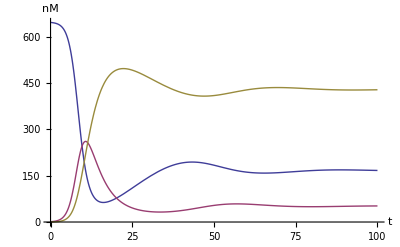

```mathematica
sol1=NDSolve[{s'[t]==(.03)*r[t]-(.0015)*s[t]*i[t], i'[t]== (.0015)*s[t]*i[t]-(.25)*i[t],r'[t]==(.25)*i[t]-(.03)*r[t], s[0]==647,i[0]==1,r[0]==0},{s,i,r},{t,0,100}]

Plot[Evaluate[{s[t],i[t],r[t]}/.sol1],{t,0,100},AxesLabel->{t,nM}]
```